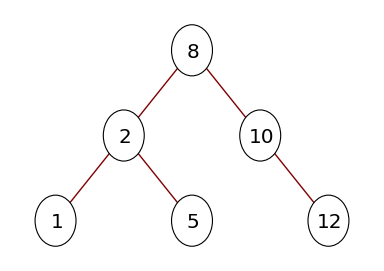

```mathematica
TreePlot[{8->2, 8->10, 2-> 1,2 -> 5, 10 -> 12},Automatic, 8, VertexLabeling->True, DirectedEdges->True,
(*VertexCoordinateRules->{8-> Automatic,2-> Automatic,1-> Automatic,5-> Automatic,10-> Automatic,9-> Automatic},*)
VertexCoordinateRules->{8->{5,5},2->{4,4},10->{6,4},12->{7,3},5->{5,3},1->{3,3}},
VertexRenderingFunction->({White,EdgeForm[{Black, Thick}],Disk[#1,.3],Black,Text[Style[#2, 20],#1 + {0.02,-0.02}]}&)]
```